```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/GeneralMetapop/Run"];
co={"../InputData/Coo100m100.txt","../InputData/Coo100m500.txt","../InputData/Coo100mAll.txt"};
(*al1 22.4 1608662 /Max[tot[[365;;453,2]]]
al0 22.4 1608662 /Max[tot[[365;;453,2]]]*)


Do[pa=Flatten[{numruns=1,maxT=26 365(*must not exceed 10585*),NumPat={100,500,40058}[[i]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.5,eA=0.95,drivertime=27 365+150,NumDriver=1000,NumDriverPat=8,d=0.005,Ld=10/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=100,al0var=0.,al1=3700,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=10,recsitesfreq=1,set=i,"e","r",start=24 365+1,co[[i]],"../InputData/RainDailyAvAv.csv","none","../InputData/arab_mortality_Jan25.csv"}];
Export["PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{i,3}];
```

```mathematica
25 365
```

9125

```mathematica
10585/365
```

29

```mathematica
start
```

8761

```mathematica
res=Import["!./gdsimsapp<PP1.csv","Table"];
```

```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/GeneralMetapop/Run/output_files"];
tot=Drop[Import["Totals1run1.txt","Table"],2];
Dimensions[tot]
```

{730,7}

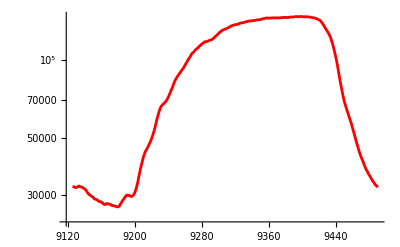

```mathematica
ListLogPlot[Table[tot[[366;;730,{1,i}]],{i,2,7,1}],PlotStyle->{Red,Blue,Green,Yellow,Orange,Purple},PlotRange->All,Joined->True]
```

```mathematica
22.4 1608662
```

3.6034×10^7

```mathematica
Max[tot[[365;;730,2]]]80
```

59045760

3687.32

184.366